## Numerical for 3 Flavor Neutrino Oscillation in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/code

Avogadro number

```mathematica
nAvo=6*10^(23)
```

600000000000000000000000

```mathematica
gF=1.17*10^(-5);
```

### Numerical

```mathematica
numDen[x_]=10^(-12-4.3 x)
```

10^(-12-4.3 x)

```mathematica
theta12=33.36/180*Pi;
theta13=8.66/180*Pi;
theta23=40/180*Pi;
deltacp=0;
(*deltacp=300/180*Pi;*)
m1sq=0.01*10^(-18);
m2sq=m1sq+0.000079*10^(-18);
m3sq=m2sq+0.0027*10^(-18);
rS = 10^(24);
omega=10^(-19);
rSomega=rS*omega;
```

```mathematica
pmns={{Cos[theta12]Cos[theta13],Sin[theta12]Cos[theta13],Sin[theta13]Exp[-I deltacp]},{-Sin[theta12]Cos[theta23]-Cos[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Cos[theta12]Cos[theta23]-Sin[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Sin[theta23]Cos[theta13]},{Sin[theta12]Sin[theta23]-Cos[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],-Cos[theta12]Sin[theta23]-Sin[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],Cos[theta23]Cos[theta13]}}
%//MatrixForm
```

{{0.82571,0.543629,0.150571},{-0.502084,0.586603,0.635459},{0.257129,-0.600304,0.757311}}

(0.82571 | 0.543629 | 0.150571
-0.502084 | 0.586603 | 0.635459
0.257129 | -0.600304 | 0.757311)

### One Method Skip

```mathematica
hamilV=rSomega pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sq}}.Transpose[pmns];
```

```mathematica
hamilM[x_]=(hamilV+rSomega{{Sqrt[2]gF numDen[x],0,0},{0,0,0},{0,0,0}})*10^(16)//Simplify
```

{{10.0864+16546.3 ⅇ^(-9.90112 x),0.291092,0.291105},{0.291092,11.1494,1.30955},{0.291105,1.30955,11.6223}}

```mathematica
nuF3M[x_]={nuF3Me[x],nuF3Mm[x],nuF3Mt[x]}
```

{nuF3Me[x],nuF3Mm[x],nuF3Mt[x]}

```mathematica
matOsc3 = I nuF3M'[x]==hamilM[x].nuF3M[x]
```

{ⅈ nuF3Me'[x],ⅈ nuF3Mm'[x],ⅈ nuF3Mt'[x]}=={(10.0864+16546.3 ⅇ^(-9.90112 x)) nuF3Me[x]+0.291092 nuF3Mm[x]+0.291105 nuF3Mt[x],0.291092 nuF3Me[x]+11.1494 nuF3Mm[x]+1.30955 nuF3Mt[x],0.291105 nuF3Me[x]+1.30955 nuF3Mm[x]+11.6223 nuF3Mt[x]}

```mathematica
sol3M=NDSolve[matOsc3&&nuF3M[0]=={1,0,0},{nuF3Me,nuF3Mm,nuF3Mt},{x,0,2000}]
```

{{nuF3Me→InterpolatingFunction[{{0., 2000.}}, <>],nuF3Mm→InterpolatingFunction[{{0., 2000.}}, <>],nuF3Mt→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
probesqrt=nuF3Me/.sol3M[[1]]
probmsqrt=nuF3Mm/.sol3M[[1]]
probtsqrt=nuF3Mt/.sol3M[[1]]
```

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

```mathematica
norm[x_]=Abs[probesqrt[x]]^2+Abs[probmsqrt[x]]^2+Abs[probtsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2

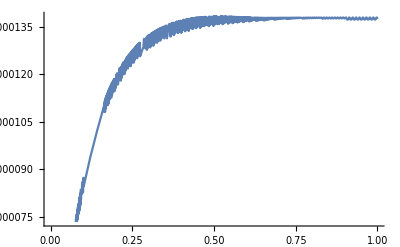

```mathematica
Plot[norm[x],{x,0,1}]
```

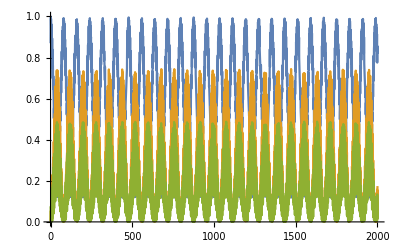

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probmsqrt[x]]^2/norm[x],Abs[probtsqrt[x]]^2/norm[x]},{x,0,2000}]
```

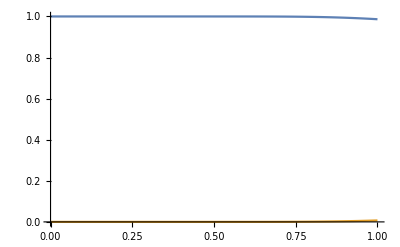

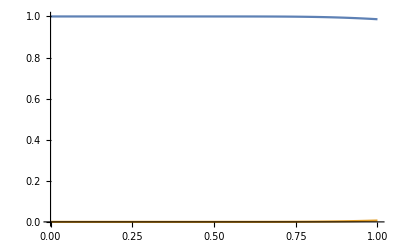

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probtsqrt[x]]^2/norm[x]},{x,0,1}]
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probmsqrt[x]]^2/norm[x]},{x,0,1}]
```

### In Vacuum Mass State Basis

```mathematica
numDen2[x_]=10^(-13-4.3 x)
```

10^(-13-4.3 x)

```mathematica
epSun= 10^(-24)
deltaH[x_]=√2 gF numDen2[x]/epSun
deltam12sq=7.6*10^(-5)*10^(-18)
deltam13sq=2.3*10^(-3)*10^(-18)
deltam23sq=deltam13sq-deltam12sq
ene=10^(-3)
```

1/1000000000000000000000000

0.0000165463 10^(11-4.3 x)

7.6×10^-23

2.3×10^-21

2.224×10^-21

1/1000

```mathematica
hamilMVM[x_]={{deltaH[x] pmns[[1,1]]^2-deltaH[x]/3+(deltam12sq+deltam13sq)/(6ene epSun),deltaH[x] pmns[[1,1]]pmns[[1,2]],deltaH[x] pmns[[1,1]] pmns[[1,3]]},{deltaH[x] pmns[[1,2]] pmns[[1,1]],deltaH[x] pmns[[1,2]]^2-deltaH[x]/3+(deltam12sq+deltam23sq)/(6ene epSun),deltaH[x]pmns[[1,2]]pmns[[1,3]]},{deltaH[x] pmns[[1,1]] pmns[[1,3]],deltaH[x] pmns[[1,2]] pmns[[1,3]],deltaH[x] pmns[[1,3]]^2-deltaH[x]/3+(deltam13sq+deltam23sq)/(6ene epSun)}}//FullSimplify
%//MatrixForm
```

{{396000.+576578. ⅇ^(-9.90112 x),742729. ⅇ^(-9.90112 x),205716. ⅇ^(-9.90112 x)},{742729. ⅇ^(-9.90112 x),383333.-62547.3 ⅇ^(-9.90112 x),135439. ⅇ^(-9.90112 x)},{205716. ⅇ^(-9.90112 x),135439. ⅇ^(-9.90112 x),754000.-514030. ⅇ^(-9.90112 x)}}

(396000.+576578. ⅇ^(-9.90112 x) | 742729. ⅇ^(-9.90112 x) | 205716. ⅇ^(-9.90112 x)
742729. ⅇ^(-9.90112 x) | 383333.-62547.3 ⅇ^(-9.90112 x) | 135439. ⅇ^(-9.90112 x)
205716. ⅇ^(-9.90112 x) | 135439. ⅇ^(-9.90112 x) | 754000.-514030. ⅇ^(-9.90112 x))

```mathematica
nuF3MVM[x_]={nuF3MVM1[x],nuF3MVM2[x],nuF3MVM3[x]}
```

{nuF3MVM1[x],nuF3MVM2[x],nuF3MVM3[x]}

```mathematica
matOsc3VM = I nuF3MVM'[x]==hamilMVM[x].nuF3MVM[x]
```

{ⅈ nuF3MVM1'[x],ⅈ nuF3MVM2'[x],ⅈ nuF3MVM3'[x]}=={(396000.+576578. ⅇ^(-9.90112 x)) nuF3MVM1[x]+742729. ⅇ^(-9.90112 x) nuF3MVM2[x]+205716. ⅇ^(-9.90112 x) nuF3MVM3[x],742729. ⅇ^(-9.90112 x) nuF3MVM1[x]+(383333.-62547.3 ⅇ^(-9.90112 x)) nuF3MVM2[x]+135439. ⅇ^(-9.90112 x) nuF3MVM3[x],205716. ⅇ^(-9.90112 x) nuF3MVM1[x]+135439. ⅇ^(-9.90112 x) nuF3MVM2[x]+(754000.-514030. ⅇ^(-9.90112 x)) nuF3MVM3[x]}

Initial conditions

```mathematica
initCon=Transpose[pmns].{1,0,0}
```

{0.82571,0.543629,0.150571}

```mathematica
sol3MVM=NDSolve[matOsc3VM&&nuF3MVM[0]==initCon,{nuF3MVM1,nuF3MVM2,nuF3MVM3},{x,0,1}]
```

{{nuF3MVM1→InterpolatingFunction[{{0., 1.}}, <>],nuF3MVM2→InterpolatingFunction[{{0., 1.}}, <>],nuF3MVM3→InterpolatingFunction[{{0., 1.}}, <>]}}

In terms of flavor eigenstates

```mathematica
prob1sqrtVM=nuF3MVM1/.sol3MVM[[1]]
prob2sqrtVM=nuF3MVM2/.sol3MVM[[1]]
prob3sqrtVM=nuF3MVM3/.sol3MVM[[1]]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

#### Diagonalize the hamiltonian

```mathematica
hamilMVM[x]//MatrixForm
```

(396000.+576578. ⅇ^(-9.90112 x) | 742729. ⅇ^(-9.90112 x) | 205716. ⅇ^(-9.90112 x)
742729. ⅇ^(-9.90112 x) | 383333.-62547.3 ⅇ^(-9.90112 x) | 135439. ⅇ^(-9.90112 x)
205716. ⅇ^(-9.90112 x) | 135439. ⅇ^(-9.90112 x) | 754000.-514030. ⅇ^(-9.90112 x))

```mathematica
hamilMVMList=Table[hamilMVM[i],{i,0,1,0.001}]
```

{{{972578.,742729.,205716.},{742729.,320786.,135439.},{205716.,135439.,239970.}},999,{{396029.,37.2246,10.3102},{37.2246,383330.,6.78803},{10.3102,6.78803,753974.}}}
 |  |  |  |

```mathematica
hamilMVMList[[1]]
```

{{972578.,742729.,205716.},{742729.,320786.,135439.},{205716.,135439.,239970.}}

```mathematica
eigenVectorsList=Table[Eigenvectors[hamilMVM[i]],{i,0,1,0.001}]
```

{{{-0.821729,-0.536914,-0.191007},{-0.161241,-0.102425,0.981586},{0.546591,-0.837396,0.00240703}},999,{{0.0000288058,0.000018317,1.},{-0.999996,-0.00293132,0.0000288594},{0.00293132,-0.999996,0.0000182325}}}
 |  |  |  |

```mathematica
diagOperatorList=Table[Transpose[eigenVectorsList[[x]]],{x,1,Length@eigenVectorsList}]
```

{{{-0.821729,-0.161241,0.546591},{-0.536914,-0.102425,-0.837396},{-0.191007,0.981586,0.00240703}},999,{{0.0000288058,-0.999996,0.00293132},{0.000018317,-0.00293132,-0.999996},{1.,0.0000288594,0.0000182325}}}
 |  |  |  |

```mathematica
(*diagOpOrthList=Table[diagOperatorList[[x]].Inverse[Sqrt[Simplify[Transpose[diagOperatorList[[x]].diagOperatorList[[x]]]]]],{x,1,Length@eigenVectorsList}] *)
```

```mathematica
Transpose[diagOperatorList[[1]]].hamilMVMList[[1]].diagOperatorList[[1]]//MatrixForm//FullSimplify
```

(1.50569×10^6 | -6.98492×10^-10 | 1.25397×10^-10
-7.27596×10^-10 | 192045. | -3.09228×10^-11
2.09184×10^-10 | -3.16049×10^-11 | -164403.)

#### Probabilities Using List

```mathematica
probsqrtDataVM=Table[{prob1sqrtVM[i],prob2sqrtVM[i],prob3sqrtVM[i]},{i,0,1,0.001}];
```

```mathematica
Export["probsqrtDataVM001-13.dat",probsqrtDataVM]
```

probsqrtDataVM001-13.dat

```mathematica
len=Length@probsqrtDataVM
```

1001

```mathematica
probsqrtVM=Table[pmns.probsqrtDataVM[[i]],{i,1,Length@probsqrtDataVM}]
```

{{1.+0. ⅈ,-8.32667×10^-17+0. ⅈ,4.16334×10^-17+0. ⅈ},{0.152522+0.986929 ⅈ,-0.0231013+0.0203811 ⅈ,-0.0259118+0.0350804 ⅈ},997,{0.134108-0.00745723 ⅈ,0.667879-0.160964 ⅈ,0.770292-0.168634 ⅈ},{0.139719-0.00261072 ⅈ,0.666013-0.157931 ⅈ,0.773275-0.161077 ⅈ}}
 |  |  |  |

```mathematica
probesqrtVM=Table[probsqrtVM[[i,1]],{i,1,Length@probsqrtDataVM}];
probmsqrtVM=Table[probsqrtVM[[i,2]],{i,1,Length@probsqrtDataVM}];
probtsqrtVM=Table[probsqrtVM[[i,3]],{i,1,Length@probsqrtDataVM}];
```

```mathematica
normVM=Table[Abs[probesqrtVM[[x]]]^2+Abs[probmsqrtVM[[x]]]^2+Abs[probtsqrtVM[[x]]]^2,{x,1,len}];
```

{1.,1.00014,1.00028,1.00041,1.00054,1.00066,1.00077,1.00087,1.00097,1.00106,1.00115,1.00124,1.00131,1.00139,1.00146,1.00156,1.00169,1.0018,1.00191,1.00201,1.00211,1.00221,1.00229,1.00238,1.00246,1.00253,1.0026,1.00267,1.00274,1.00282,1.00294,1.00304,1.00315,1.00324,1.00333,1.00342,1.0035,1.00358,1.00365,1.00372,1.00379,1.00385,1.00391,1.00397,1.00406,1.00416,1.00426,1.00435,1.00444,1.00452,1.0046,1.00467,1.00475,1.00481,1.00488,1.00494,1.005,1.00506,1.00511,1.00516,1.00526,1.00534,1.00543,1.00552,1.00559,1.00567,1.00574,1.00581,1.00588,1.00594,1.006,1.00606,1.00611,1.00616,1.00622,1.00626,1.00631,1.0064,1.00648,1.00656,1.00663,1.00671,1.00678,1.00684,1.00691,1.00697,1.00703,1.00708,1.00714,1.00719,1.00724,1.00729,1.00734,1.00738,1.00742,1.00747,1.00755,1.00762,1.0077,1.00776,1.00783,1.00789,1.00795,1.00801,1.00807,1.00813,1.00818,1.00823,1.00828,1.00833,1.00837,1.00842,1.00846,1.0085,1.00854,1.00858,1.00862,1.00867,1.00874,1.0088,1.00887,1.00893,1.00899,1.00905,1.00911,1.00917,1.00922,1.00927,1.00933,1.00938,1.00942,1.00947,1.00952,1.00956,1.00961,1.00965,1.00969,1.00973,1.00977,1.00981,1.00985,1.00989,1.00992,1.00996,1.00999,1.01003,1.01006,1.0101,1.01013,1.01018,1.01024,1.01031,1.01037,1.01043,1.01049,1.01055,1.01061,1.01067,1.01073,1.01079,1.01084,1.0109,1.01096,1.01102,1.01107,1.01113,1.01119,1.01124,1.0113,1.01135,1.01141,1.01147,1.01152,1.01158,1.01163,1.01169,1.01175,1.0118,1.01186,1.01192,1.01197,1.01203,1.01209,1.01215,1.01221,1.01226,1.01232,1.01238,1.01244,1.0125,1.01256,1.01262,1.01268,1.01274,1.0128,1.01286,1.01292,1.01298,1.01305,1.01311,1.01317,1.01323,1.01329,1.01336,1.01342,1.01349,1.01355,1.01362,1.01368,1.01375,1.01381,1.01388,1.01395,1.01402,1.01408,1.01415,1.01422,1.01429,1.01436,1.01442,1.0145,1.01457,1.01463,1.01471,1.01478,1.01485,1.01492,1.01499,1.01507,1.01514,1.01521,1.01529,1.01536,1.01544,1.01551,1.01559,1.01567,1.01574,1.01582,1.01589,1.01597,1.01605,1.01613,1.01621,1.01628,1.01636,1.01644,1.01652,1.01661,1.01668,1.01677,1.01685,1.01693,1.01701,1.01709,1.01718,1.01726,1.01734,1.01743,1.01751,1.0176,1.01768,1.01776,1.01785,1.01793,1.01802,1.01811,1.01819,1.01829,1.01837,1.01846,1.01855,1.01863,1.01873,1.01881,1.0189,1.01899,1.01908,1.01918,1.01926,1.01936,1.01945,1.01954,1.01963,1.01972,1.01982,1.01991,1.02,1.0201,1.02019,1.02029,1.02038,1.02047,1.02057,1.02066,1.02076,1.02086,1.02095,1.02105,1.02114,1.02124,1.02134,1.02144,1.02154,1.02163,1.02173,1.02183,1.02193,1.02203,1.02213,1.02223,1.02233,1.02243,1.02253,1.02263,1.02273,1.02283,1.02293,1.02304,1.02314,1.02324,1.02334,1.02345,1.02355,1.02365,1.02376,1.02386,1.02396,1.02407,1.02417,1.02428,1.02438,1.02449,1.0246,1.0247,1.02481,1.02491,1.02502,1.02513,1.02523,1.02534,1.02544,1.02555,1.02566,1.02576,1.02588,1.02598,1.02609,1.0262,1.02631,1.02642,1.02653,1.02664,1.02675,1.02685,1.02697,1.02708,1.02719,1.0273,1.02741,1.02752,1.02763,1.02774,1.02785,1.02796,1.02808,1.02819,1.0283,1.02841,1.02852,1.02864,1.02875,1.02886,1.02898,1.02909,1.02921,1.02932,1.02943,1.02955,1.02966,1.02978,1.02989,1.03,1.03012,1.03023,1.03035,1.03046,1.03058,1.0307,1.03081,1.03093,1.03104,1.03116,1.03128,1.03139,1.03151,1.03162,1.03174,1.03186,1.03197,1.0321,1.03221,1.03233,1.03245,1.03256,1.03268,1.0328,1.03292,1.03304,1.03315,1.03328,1.03339,1.03351,1.03363,1.03375,1.03387,1.03398,1.03411,1.03423,1.03434,1.03447,1.03458,1.03471,1.03483,1.03494,1.03507,1.03518,1.03531,1.03543,1.03555,1.03567,1.03579,1.03591,1.03603,1.03615,1.03628,1.0364,1.03652,1.03664,1.03676,1.03689,1.03701,1.03713,1.03725,1.03737,1.0375,1.03762,1.03774,1.03787,1.03799,1.03811,1.03823,1.03836,1.03848,1.0386,1.03873,1.03885,1.03898,1.0391,1.03922,1.03935,1.03947,1.0396,1.03972,1.03984,1.03997,1.04009,1.04022,1.04034,1.04046,1.04059,1.04071,1.04084,1.04096,1.04109,1.04122,1.04134,1.04147,1.04159,1.04171,1.04184,1.04196,1.04209,1.04222,1.04234,1.04247,1.04259,1.04272,1.04285,1.04297,1.0431,1.04322,1.04335,1.04348,1.0436,1.04373,1.04385,1.04399,1.04411,1.04424,1.04437,1.04449,1.04462,1.04474,1.04487,1.045,1.04512,1.04526,1.04538,1.04551,1.04564,1.04576,1.04589,1.04602,1.04615,1.04628,1.0464,1.04653,1.04666,1.04679,1.04692,1.04704,1.04717,1.0473,1.04743,1.04756,1.04768,1.04782,1.04794,1.04807,1.0482,1.04833,1.04846,1.04858,1.04871,1.04884,1.04897,1.0491,1.04923,1.04936,1.04949,1.04961,1.04975,1.04987,1.05001,1.05014,1.05026,1.0504,1.05052,1.05065,1.05078,1.05091,1.05104,1.05117,1.0513,1.05143,1.05156,1.05169,1.05182,1.05195,1.05208,1.05221,1.05234,1.05247,1.0526,1.05273,1.05286,1.053,1.05312,1.05325,1.05339,1.05351,1.05365,1.05377,1.05391,1.05404,1.05417,1.0543,1.05443,1.05456,1.05469,1.05482,1.05496,1.05508,1.05522,1.05535,1.05548,1.05561,1.05574,1.05587,1.056,1.05613,1.05627,1.05639,1.05653,1.05666,1.05679,1.05693,1.05705,1.05719,1.05732,1.05745,1.05758,1.05771,1.05785,1.05798,1.05811,1.05824,1.05837,1.05851,1.05864,1.05877,1.0589,1.05903,1.05917,1.0593,1.05943,1.05957,1.05969,1.05983,1.05996,1.06009,1.06023,1.06035,1.06049,1.06062,1.06075,1.06089,1.06102,1.06115,1.06128,1.06142,1.06155,1.06168,1.06182,1.06195,1.06208,1.06222,1.06234,1.06248,1.06261,1.06274,1.06288,1.06301,1.06315,1.06328,1.06341,1.06355,1.06367,1.06381,1.06394,1.06408,1.06421,1.06434,1.06448,1.06461,1.06474,1.06488,1.06501,1.06515,1.06528,1.06541,1.06555,1.06568,1.06581,1.06594,1.06608,1.06622,1.06634,1.06648,1.06661,1.06675,1.06688,1.06701,1.06715,1.06728,1.06742,1.06755,1.06768,1.06782,1.06795,1.06809,1.06822,1.06835,1.06849,1.06862,1.06876,1.0689,1.06902,1.06916,1.06929,1.06943,1.06957,1.0697,1.06984,1.06997,1.0701,1.07024,1.07037,1.07051,1.07064,1.07078,1.07091,1.07104,1.07118,1.07131,1.07145,1.07158,1.07172,1.07186,1.07199,1.07212,1.07226,1.07239,1.07253,1.07266,1.0728,1.07293,1.07306,1.07321,1.07334,1.07347,1.07361,1.07374,1.07388,1.07401,1.07415,1.07428,1.07442,1.07456,1.07469,1.07482,1.07496,1.07509,1.07523,1.07536,1.0755,1.07564,1.07577,1.07591,1.07604,1.07618,1.07631,1.07645,1.07659,1.07672,1.07686,1.07699,1.07713,1.07727,1.0774,1.07754,1.07767,1.0778,1.07794,1.07808,1.07821,1.07835,1.07848,1.07862,1.07875,1.07889,1.07903,1.07916,1.0793,1.07943,1.07957,1.07971,1.07984,1.07998,1.08011,1.08025,1.08039,1.08052,1.08067,1.0808,1.08094,1.08107,1.08121,1.08135,1.08148,1.08162,1.08175,1.08189,1.08203,1.08216,1.0823,1.08243,1.08257,1.08271,1.08284,1.08298,1.08312,1.08325,1.08339,1.08352,1.08367,1.0838,1.08394,1.08408,1.08421,1.08435,1.08448,1.08462,1.08476,1.08489,1.08503,1.08517,1.0853,1.08544,1.08558,1.08572,1.08585,1.08599,1.08613,1.08626,1.0864,1.08654,1.08667,1.08681,1.08695,1.08709,1.08722,1.08736,1.0875,1.08763,1.08778,1.08791,1.08805,1.08819,1.08832,1.08846,1.0886,1.08873,1.08887,1.08901,1.08915,1.08928,1.08942,1.08956,1.08969,1.08984,1.08997,1.09011,1.09025,1.09038,1.09052,1.09066,1.0908,1.09094,1.09107,1.09121,1.09135,1.09149,1.09163,1.09176,1.0919,1.09204,1.09218,1.09231,1.09245,1.09259,1.09272,1.09286,1.093,1.09314,1.09328,1.09341,1.09356,1.09369,1.09383,1.09397,1.09411,1.09425,1.09438,1.09452,1.09466,1.0948,1.09494,1.09508,1.09521,1.09535,1.09549,1.09563,1.09577,1.0959,1.09605,1.09618,1.09632,1.09646,1.09659,1.09674,1.09687,1.09701,1.09715,1.09729,1.09743,1.09756,1.09771,1.09784,1.09798,1.09812,1.09826,1.0984,1.09854,1.09867,1.09882,1.09895,1.09909,1.09923,1.09937,1.09951,1.09965,1.09979,1.09993,1.10006,1.10021,1.10034,1.10048,1.10062,1.10076,1.1009,1.10104,1.10118,1.10132,1.10145,1.1016,1.10173,1.10187,1.10201,1.10215,1.10229,1.10243,1.10257,1.10271,1.10285,1.10299,1.10312,1.10327,1.1034,1.10354,1.10369,1.10382,1.10396,1.1041,1.10424,1.10438,1.10452,1.10466,1.1048,1.10494,1.10508,1.10522,1.10536,1.1055,1.10564,1.10578,1.10591,1.10606,1.1062,1.10633,1.10648,1.10661,1.10676,1.10689,1.10703,1.10718,1.10731,1.10746,1.10759,1.10773,1.10788,1.10801,1.10816,1.10829,1.10843,1.10858,1.10871,1.10886,1.10899,1.10913,1.10928,1.10941,1.10956,1.10969,1.10983,1.10998,1.11011,1.11026,1.1104,1.11054,1.11068,1.11081,1.11096,1.1111,1.11124,1.11138,1.11152,1.11166,1.1118,1.11194}

```mathematica
normVM[[2]]//N
```

1.00014

```mathematica
normVMList=Table[{i/len,normVM[[i]]},{i,1,len}];
```

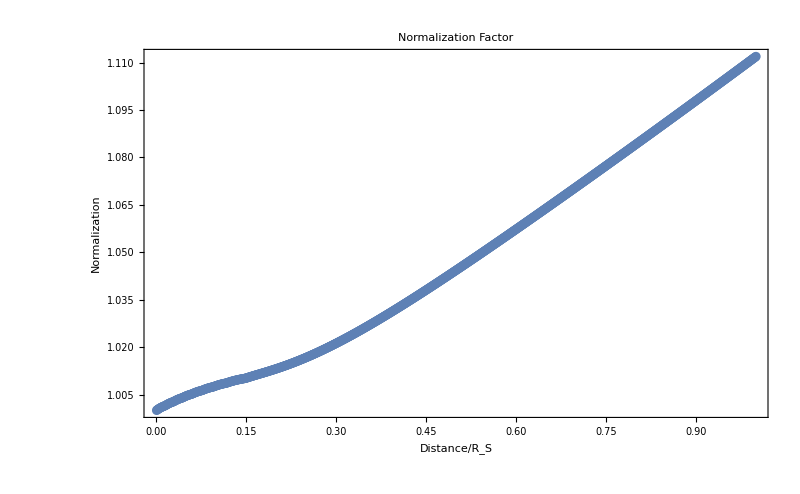

```mathematica
ListPlot[normVMList,Frame->True,ImageSize->800,PlotLabel->"Normalization Factor",FrameLabel->{"Distance/R_S","Normalization"}]
```

```mathematica
probesqrtVMList=Table[{x/len,Abs[probesqrtVM[[x]]]^2/normVM[[x]]},{x,1,len}];
probmsqrtVMList=Table[{x/len,Abs[probmsqrtVM[[x]]]^2/normVM[[x]]},{x,1,len}];
probtsqrtVMList=Table[{x/len,Abs[probtsqrtVM[[x]]]^2/normVM[[x]]},{x,1,len}];
```

```mathematica
ListPlot[{probesqrtVMList,probmsqrtVMList,probtsqrtVMList},PlotLabel->"Probability for Different Neutrino Flavors",Frame->True,ImageSize->800,Joined->True,PlotLegends->Placed[{"ν_e","ν_μ","ν_τ"},{Center,Above}]]
```

-Graphics-

### Extract Probabilities

```mathematica
probsqrtVM=pmns.{prob1sqrtVM,prob2sqrtVM,prob3sqrtVM}
```

{0.150571 InterpolatingFunction[{{0., 1.}}, <>]+0.543629 InterpolatingFunction[{{0., 1.}}, <>]+0.82571 InterpolatingFunction[{{0., 1.}}, <>],0.635459 InterpolatingFunction[{{0., 1.}}, <>]+0.586603 InterpolatingFunction[{{0., 1.}}, <>]-0.502084 InterpolatingFunction[{{0., 1.}}, <>],0.757311 InterpolatingFunction[{{0., 1.}}, <>]-0.600304 InterpolatingFunction[{{0., 1.}}, <>]+0.257129 InterpolatingFunction[{{0., 1.}}, <>]}

```mathematica
normVM[x_]=Abs[probsqrtVM[[1]][x]]^2+Abs[probsqrtVM[[2]][x]]^2+Abs[probsqrtVM[[3]][x]]^2
```

Set::write: Tag List in {1., 1.00014, 1.00028, 1.00041, 1.00054, 1.00066, 1.00077, 1.00087, 1.00097, 1.00106, 1.00115, 1.00124, 1.00131, 1.00139, « 24 », 1.00365, 1.00372, 1.00379, 1.00385, 1.00391, 1.00397, 1.00406, 1.00416, 1.00426, 1.00435, 1.00444, 1.00452, « 951 »}[x_] is Protected.

Abs[(0.635459 InterpolatingFunction[{{0., 1.}}, <>]+0.586603 InterpolatingFunction[{{0., 1.}}, <>]-0.502084 InterpolatingFunction[{{0., 1.}}, <>])[x]]^2+Abs[(0.757311 InterpolatingFunction[{{0., 1.}}, <>]-0.600304 InterpolatingFunction[{{0., 1.}}, <>]+0.257129 InterpolatingFunction[{{0., 1.}}, <>])[x]]^2+Abs[(0.150571 InterpolatingFunction[{{0., 1.}}, <>]+0.543629 InterpolatingFunction[{{0., 1.}}, <>]+0.82571 InterpolatingFunction[{{0., 1.}}, <>])[x]]^2

```mathematica
normVM[0.5]
```

{1.,1.00014,1.00028,1.00041,1.00054,1.00066,1.00077,1.00087,1.00097,1.00106,1.00115,1.00124,1.00131,1.00139,1.00146,1.00156,1.00169,1.0018,1.00191,1.00201,1.00211,1.00221,1.00229,1.00238,1.00246,1.00253,1.0026,1.00267,1.00274,1.00282,1.00294,1.00304,1.00315,1.00324,1.00333,1.00342,1.0035,1.00358,1.00365,1.00372,1.00379,1.00385,1.00391,1.00397,1.00406,1.00416,1.00426,1.00435,1.00444,1.00452,1.0046,1.00467,1.00475,1.00481,1.00488,1.00494,1.005,1.00506,1.00511,1.00516,1.00526,1.00534,1.00543,1.00552,1.00559,1.00567,1.00574,1.00581,1.00588,1.00594,1.006,1.00606,1.00611,1.00616,1.00622,1.00626,1.00631,1.0064,1.00648,1.00656,1.00663,1.00671,1.00678,1.00684,1.00691,1.00697,1.00703,1.00708,1.00714,1.00719,1.00724,1.00729,1.00734,1.00738,1.00742,1.00747,1.00755,1.00762,1.0077,1.00776,1.00783,1.00789,1.00795,1.00801,1.00807,1.00813,1.00818,1.00823,1.00828,1.00833,1.00837,1.00842,1.00846,1.0085,1.00854,1.00858,1.00862,1.00867,1.00874,1.0088,1.00887,1.00893,1.00899,1.00905,1.00911,1.00917,1.00922,1.00927,1.00933,1.00938,1.00942,1.00947,1.00952,1.00956,1.00961,1.00965,1.00969,1.00973,1.00977,1.00981,1.00985,1.00989,1.00992,1.00996,1.00999,1.01003,1.01006,1.0101,1.01013,1.01018,1.01024,1.01031,1.01037,1.01043,1.01049,1.01055,1.01061,1.01067,1.01073,1.01079,1.01084,1.0109,1.01096,1.01102,1.01107,1.01113,1.01119,1.01124,1.0113,1.01135,1.01141,1.01147,1.01152,1.01158,1.01163,1.01169,1.01175,1.0118,1.01186,1.01192,1.01197,1.01203,1.01209,1.01215,1.01221,1.01226,1.01232,1.01238,1.01244,1.0125,1.01256,1.01262,1.01268,1.01274,1.0128,1.01286,1.01292,1.01298,1.01305,1.01311,1.01317,1.01323,1.01329,1.01336,1.01342,1.01349,1.01355,1.01362,1.01368,1.01375,1.01381,1.01388,1.01395,1.01402,1.01408,1.01415,1.01422,1.01429,1.01436,1.01442,1.0145,1.01457,1.01463,1.01471,1.01478,1.01485,1.01492,1.01499,1.01507,1.01514,1.01521,1.01529,1.01536,1.01544,1.01551,1.01559,1.01567,1.01574,1.01582,1.01589,1.01597,1.01605,1.01613,1.01621,1.01628,1.01636,1.01644,1.01652,1.01661,1.01668,1.01677,1.01685,1.01693,1.01701,1.01709,1.01718,1.01726,1.01734,1.01743,1.01751,1.0176,1.01768,1.01776,1.01785,1.01793,1.01802,1.01811,1.01819,1.01829,1.01837,1.01846,1.01855,1.01863,1.01873,1.01881,1.0189,1.01899,1.01908,1.01918,1.01926,1.01936,1.01945,1.01954,1.01963,1.01972,1.01982,1.01991,1.02,1.0201,1.02019,1.02029,1.02038,1.02047,1.02057,1.02066,1.02076,1.02086,1.02095,1.02105,1.02114,1.02124,1.02134,1.02144,1.02154,1.02163,1.02173,1.02183,1.02193,1.02203,1.02213,1.02223,1.02233,1.02243,1.02253,1.02263,1.02273,1.02283,1.02293,1.02304,1.02314,1.02324,1.02334,1.02345,1.02355,1.02365,1.02376,1.02386,1.02396,1.02407,1.02417,1.02428,1.02438,1.02449,1.0246,1.0247,1.02481,1.02491,1.02502,1.02513,1.02523,1.02534,1.02544,1.02555,1.02566,1.02576,1.02588,1.02598,1.02609,1.0262,1.02631,1.02642,1.02653,1.02664,1.02675,1.02685,1.02697,1.02708,1.02719,1.0273,1.02741,1.02752,1.02763,1.02774,1.02785,1.02796,1.02808,1.02819,1.0283,1.02841,1.02852,1.02864,1.02875,1.02886,1.02898,1.02909,1.02921,1.02932,1.02943,1.02955,1.02966,1.02978,1.02989,1.03,1.03012,1.03023,1.03035,1.03046,1.03058,1.0307,1.03081,1.03093,1.03104,1.03116,1.03128,1.03139,1.03151,1.03162,1.03174,1.03186,1.03197,1.0321,1.03221,1.03233,1.03245,1.03256,1.03268,1.0328,1.03292,1.03304,1.03315,1.03328,1.03339,1.03351,1.03363,1.03375,1.03387,1.03398,1.03411,1.03423,1.03434,1.03447,1.03458,1.03471,1.03483,1.03494,1.03507,1.03518,1.03531,1.03543,1.03555,1.03567,1.03579,1.03591,1.03603,1.03615,1.03628,1.0364,1.03652,1.03664,1.03676,1.03689,1.03701,1.03713,1.03725,1.03737,1.0375,1.03762,1.03774,1.03787,1.03799,1.03811,1.03823,1.03836,1.03848,1.0386,1.03873,1.03885,1.03898,1.0391,1.03922,1.03935,1.03947,1.0396,1.03972,1.03984,1.03997,1.04009,1.04022,1.04034,1.04046,1.04059,1.04071,1.04084,1.04096,1.04109,1.04122,1.04134,1.04147,1.04159,1.04171,1.04184,1.04196,1.04209,1.04222,1.04234,1.04247,1.04259,1.04272,1.04285,1.04297,1.0431,1.04322,1.04335,1.04348,1.0436,1.04373,1.04385,1.04399,1.04411,1.04424,1.04437,1.04449,1.04462,1.04474,1.04487,1.045,1.04512,1.04526,1.04538,1.04551,1.04564,1.04576,1.04589,1.04602,1.04615,1.04628,1.0464,1.04653,1.04666,1.04679,1.04692,1.04704,1.04717,1.0473,1.04743,1.04756,1.04768,1.04782,1.04794,1.04807,1.0482,1.04833,1.04846,1.04858,1.04871,1.04884,1.04897,1.0491,1.04923,1.04936,1.04949,1.04961,1.04975,1.04987,1.05001,1.05014,1.05026,1.0504,1.05052,1.05065,1.05078,1.05091,1.05104,1.05117,1.0513,1.05143,1.05156,1.05169,1.05182,1.05195,1.05208,1.05221,1.05234,1.05247,1.0526,1.05273,1.05286,1.053,1.05312,1.05325,1.05339,1.05351,1.05365,1.05377,1.05391,1.05404,1.05417,1.0543,1.05443,1.05456,1.05469,1.05482,1.05496,1.05508,1.05522,1.05535,1.05548,1.05561,1.05574,1.05587,1.056,1.05613,1.05627,1.05639,1.05653,1.05666,1.05679,1.05693,1.05705,1.05719,1.05732,1.05745,1.05758,1.05771,1.05785,1.05798,1.05811,1.05824,1.05837,1.05851,1.05864,1.05877,1.0589,1.05903,1.05917,1.0593,1.05943,1.05957,1.05969,1.05983,1.05996,1.06009,1.06023,1.06035,1.06049,1.06062,1.06075,1.06089,1.06102,1.06115,1.06128,1.06142,1.06155,1.06168,1.06182,1.06195,1.06208,1.06222,1.06234,1.06248,1.06261,1.06274,1.06288,1.06301,1.06315,1.06328,1.06341,1.06355,1.06367,1.06381,1.06394,1.06408,1.06421,1.06434,1.06448,1.06461,1.06474,1.06488,1.06501,1.06515,1.06528,1.06541,1.06555,1.06568,1.06581,1.06594,1.06608,1.06622,1.06634,1.06648,1.06661,1.06675,1.06688,1.06701,1.06715,1.06728,1.06742,1.06755,1.06768,1.06782,1.06795,1.06809,1.06822,1.06835,1.06849,1.06862,1.06876,1.0689,1.06902,1.06916,1.06929,1.06943,1.06957,1.0697,1.06984,1.06997,1.0701,1.07024,1.07037,1.07051,1.07064,1.07078,1.07091,1.07104,1.07118,1.07131,1.07145,1.07158,1.07172,1.07186,1.07199,1.07212,1.07226,1.07239,1.07253,1.07266,1.0728,1.07293,1.07306,1.07321,1.07334,1.07347,1.07361,1.07374,1.07388,1.07401,1.07415,1.07428,1.07442,1.07456,1.07469,1.07482,1.07496,1.07509,1.07523,1.07536,1.0755,1.07564,1.07577,1.07591,1.07604,1.07618,1.07631,1.07645,1.07659,1.07672,1.07686,1.07699,1.07713,1.07727,1.0774,1.07754,1.07767,1.0778,1.07794,1.07808,1.07821,1.07835,1.07848,1.07862,1.07875,1.07889,1.07903,1.07916,1.0793,1.07943,1.07957,1.07971,1.07984,1.07998,1.08011,1.08025,1.08039,1.08052,1.08067,1.0808,1.08094,1.08107,1.08121,1.08135,1.08148,1.08162,1.08175,1.08189,1.08203,1.08216,1.0823,1.08243,1.08257,1.08271,1.08284,1.08298,1.08312,1.08325,1.08339,1.08352,1.08367,1.0838,1.08394,1.08408,1.08421,1.08435,1.08448,1.08462,1.08476,1.08489,1.08503,1.08517,1.0853,1.08544,1.08558,1.08572,1.08585,1.08599,1.08613,1.08626,1.0864,1.08654,1.08667,1.08681,1.08695,1.08709,1.08722,1.08736,1.0875,1.08763,1.08778,1.08791,1.08805,1.08819,1.08832,1.08846,1.0886,1.08873,1.08887,1.08901,1.08915,1.08928,1.08942,1.08956,1.08969,1.08984,1.08997,1.09011,1.09025,1.09038,1.09052,1.09066,1.0908,1.09094,1.09107,1.09121,1.09135,1.09149,1.09163,1.09176,1.0919,1.09204,1.09218,1.09231,1.09245,1.09259,1.09272,1.09286,1.093,1.09314,1.09328,1.09341,1.09356,1.09369,1.09383,1.09397,1.09411,1.09425,1.09438,1.09452,1.09466,1.0948,1.09494,1.09508,1.09521,1.09535,1.09549,1.09563,1.09577,1.0959,1.09605,1.09618,1.09632,1.09646,1.09659,1.09674,1.09687,1.09701,1.09715,1.09729,1.09743,1.09756,1.09771,1.09784,1.09798,1.09812,1.09826,1.0984,1.09854,1.09867,1.09882,1.09895,1.09909,1.09923,1.09937,1.09951,1.09965,1.09979,1.09993,1.10006,1.10021,1.10034,1.10048,1.10062,1.10076,1.1009,1.10104,1.10118,1.10132,1.10145,1.1016,1.10173,1.10187,1.10201,1.10215,1.10229,1.10243,1.10257,1.10271,1.10285,1.10299,1.10312,1.10327,1.1034,1.10354,1.10369,1.10382,1.10396,1.1041,1.10424,1.10438,1.10452,1.10466,1.1048,1.10494,1.10508,1.10522,1.10536,1.1055,1.10564,1.10578,1.10591,1.10606,1.1062,1.10633,1.10648,1.10661,1.10676,1.10689,1.10703,1.10718,1.10731,1.10746,1.10759,1.10773,1.10788,1.10801,1.10816,1.10829,1.10843,1.10858,1.10871,1.10886,1.10899,1.10913,1.10928,1.10941,1.10956,1.10969,1.10983,1.10998,1.11011,1.11026,1.1104,1.11054,1.11068,1.11081,1.11096,1.1111,1.11124,1.11138,1.11152,1.11166,1.1118,1.11194}[0.5]

### Ternary Diagram

```mathematica
probesqrtVMList=Table[{x/len,Abs[probesqrtVM[[x]]]^2/normVM[[x]]},{x,1,len}];
probmsqrtVMList=Table[{x/len,Abs[probmsqrtVM[[x]]]^2/normVM[[x]]},{x,1,len}];
probtsqrtVMList=Table[{x/len,Abs[probtsqrtVM[[x]]]^2/normVM[[x]]},{x,1,len}];
```

```mathematica
ternaryData=Table[{probesqrtVMList[[x,2]],probmsqrtVMList[[x,2]],probtsqrtVMList[[x,2]]},{x,1,len}];
```

```mathematica
Export["data/ternaryData3MSW-minus13-e-1.txt",ternaryData,"CSV"]
```

ternaryData3MSW-minus14-e-1.txt

Vacuum Mass eigenstates

```mathematica
Abs[probsqrtDataVM[[100,1]]]^2
```

0.652653

```mathematica
normVMVacEigen=Table[Abs[probsqrtDataVM[[x,1]]]^2+Abs[probsqrtDataVM[[x,2]]]^2+Abs[probsqrtDataVM[[x,3]]]^2,{x,1,len}];
```

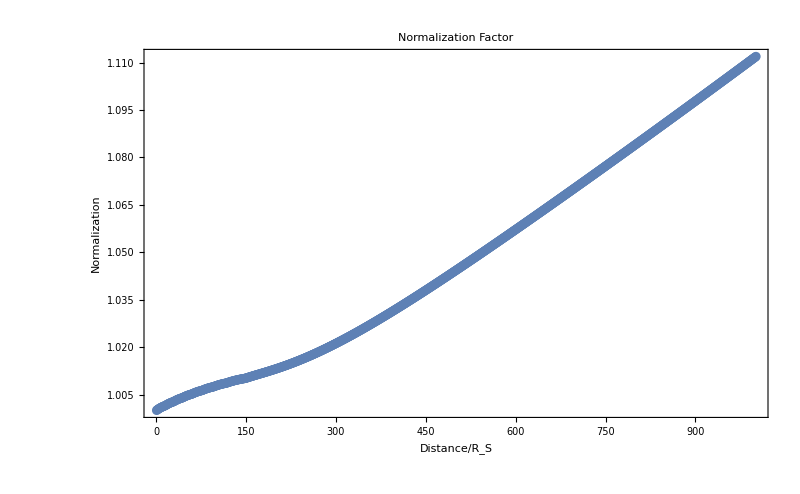

```mathematica
ListPlot[normVMVacEigen,Frame->True,ImageSize->800,PlotLabel->"Normalization Factor",FrameLabel->{"Distance/R_S","Normalization"}]
```

```mathematica
prob1sqrtVMList=Table[Abs[probsqrtDataVM[[i,1]]]^2/normVM[[i]],{i,1,Length@probsqrtDataVM}];
prob2sqrtVMList=Table[Abs[probsqrtDataVM[[i,2]]]^2/normVM[[i]],{i,1,Length@probsqrtDataVM}];
prob3sqrtVMList=Table[Abs[probsqrtDataVM[[i,3]]]^2/normVM[[i]],{i,1,Length@probsqrtDataVM}];
```

```mathematica
ListPlot[{prob1sqrtVMList,prob2sqrtVMList,prob3sqrtVMList},PlotLabel->"Probability for Different Neutrino Vacuum Eigenstates",Frame->True,ImageSize->800,Joined->True,PlotLegends->{Placed[{"ν_v1","ν_v2","ν_v3"},{Center,Above}]}]
```

-Graphics-

```mathematica
ternaryDataVacEigen=Table[{Abs[probsqrtDataVM[[x,1]]]^2/normVMVacEigen[[x]],Abs[probsqrtDataVM[[x,2]]]^2/normVMVacEigen[[x]],Abs[probsqrtDataVM[[x,3]]]^2/normVMVacEigen[[x]]},{x,1,1000}];
```

```mathematica
Export["data/ternaryData3MSW-VacEigen-minus13-e-1.txt",ternaryDataVacEigen,"CSV"]
```

data/ternaryData3MSW-VacEigen-minus13-e-1.txt

In instantaneous eigenstates of the hamiltonian

```mathematica
Transpose[diagOperatorList[[2]]].probsqrtDataVM[[2]]
%//MatrixForm
```

{-0.150951-0.987756 ⅈ,-0.0410071-0.00107576 ⅈ,0.000391504+0.00352268 ⅈ}

(-0.150951-0.987756 ⅈ
-0.0410071-0.00107576 ⅈ
0.000391504+0.00352268 ⅈ)

```mathematica
probsqrtInstDataVM=Table[Transpose[diagOperatorList[[x]]].probsqrtDataVM[[x]],{x,1,len}]
```

{{-0.999152+0. ⅈ,-0.0410216+0. ⅈ,-0.00354437+0. ⅈ},{-0.150951-0.987756 ⅈ,-0.0410071-0.00107576 ⅈ,0.000391504+0.00352268 ⅈ},997,{1.02795-0.231116 ⅈ,0.0265562-0.0313141 ⅈ,-0.00233515-0.00266713 ⅈ},{1.02987-0.222736 ⅈ,0.0202188-0.0357352 ⅈ,-0.00248018-0.00253283 ⅈ}}
 |  |  |  |

```mathematica
probInst1sqrtVMList=Table[Abs[probsqrtInstDataVM[[i,1]]]^2,{i,1,Length@probsqrtInstDataVM}];
probInst2sqrtVMList=Table[Abs[probsqrtInstDataVM[[i,2]]]^2,{i,1,Length@probsqrtInstDataVM}];
probInst3sqrtVMList=Table[Abs[probsqrtInstDataVM[[i,3]]]^2,{i,1,Length@probsqrtInstDataVM}];
```

```mathematica
normVMInstEigen=Table[Abs[probsqrtInstDataVM[[x,1]]]^2+Abs[probsqrtInstDataVM[[x,2]]]^2+Abs[probsqrtInstDataVM[[x,3]]]^2,{x,1,len}];
```

```mathematica
ternaryDataInstEigen=Table[{Abs[probsqrtInstDataVM[[x,1]]]^2/normVMInstEigen[[x]],Abs[probsqrtInstDataVM[[x,2]]]^2/normVMInstEigen[[x]],Abs[probsqrtInstDataVM[[x,3]]]^2/normVMInstEigen[[x]]},{x,1,len}];
```

```mathematica
Export["data/ternaryData3MSW-InstEigen-minus13-e-1.txt",ternaryDataInstEigen,"CSV"]
```

data/ternaryData3MSW-InstEigen-minus13-e-1.txt

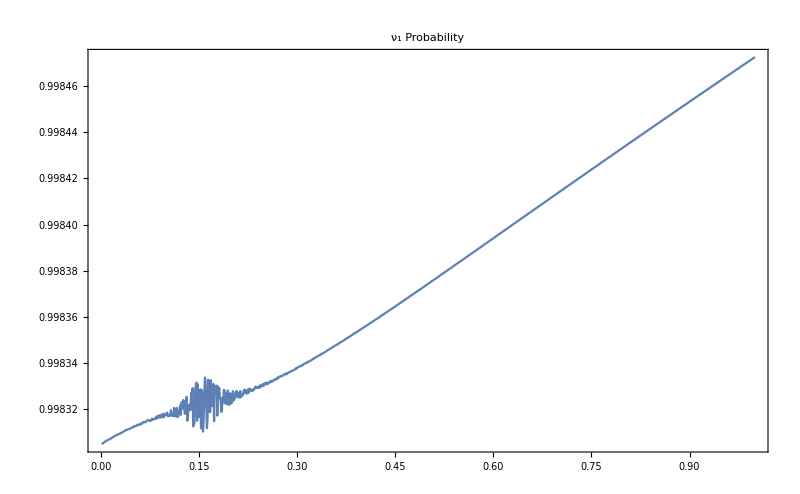

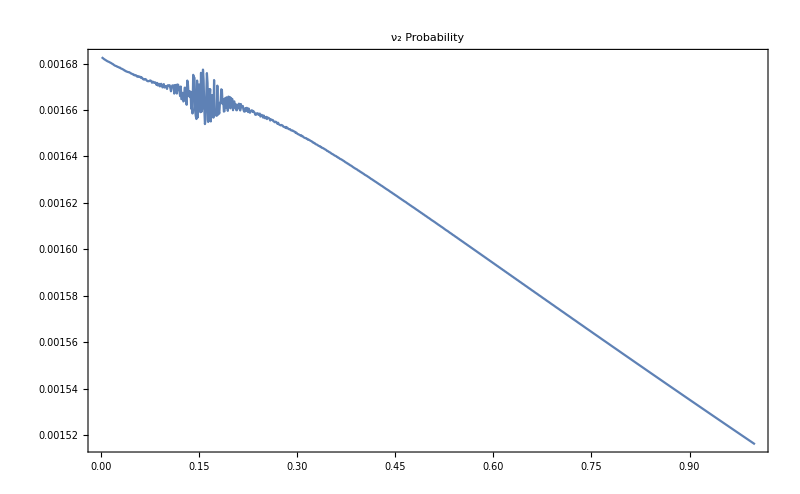

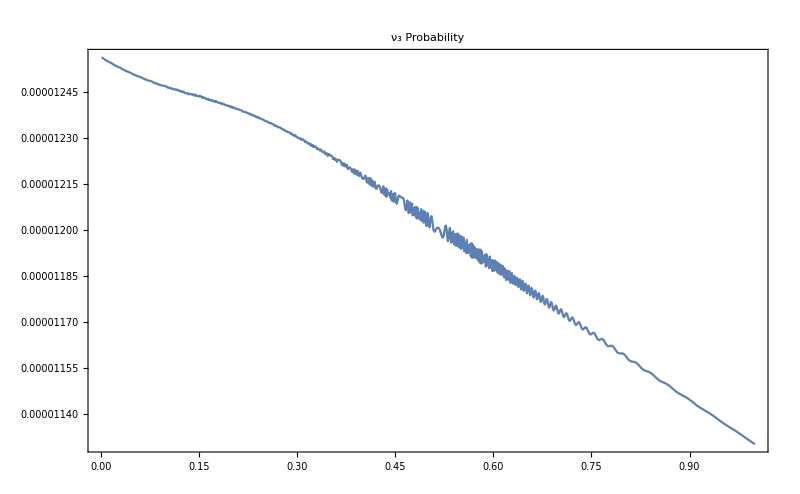

```mathematica
ListPlot[{Table[{x/len,ternaryDataInstEigen[[x,1]]},{x,1,len}]},Joined->True,Frame->True,ImageSize->800,PlotLabel->"ν_1 Probability"]
ListPlot[{Table[{x/len,ternaryDataInstEigen[[x,2]]},{x,1,len}]},Joined->True,Frame->True,ImageSize->800,PlotLabel->"ν_2 Probability"]
ListPlot[{Table[{x/len,ternaryDataInstEigen[[x,3]]},{x,1,len}]},Joined->True,Frame->True,ImageSize->800,PlotLabel->"ν_3 Probability"]
```

### Test Function

```mathematica
testFunction1[x_]=395999.99999999994+5.765775601702067*^6 ⅇ^(-9.901115899874396 x)
testFunction2[x_]=383333.3333333333-625472.6325272891 ⅇ^(-9.901115899874396 x)
testFunction3[x_]=754000.-5.140302969174778*^6 ⅇ^(-9.901115899874396 x)
```

396000.+5.76578×10^6 ⅇ^(-9.90112 x)

383333.-625473. ⅇ^(-9.90112 x)

754000.-5.1403×10^6 ⅇ^(-9.90112 x)

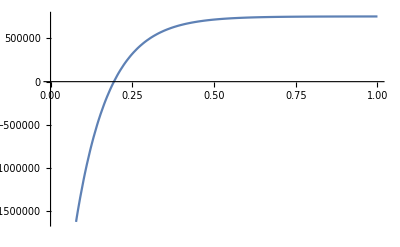

```mathematica
Plot[testFunction3[x],{x,0,1}]
```